## Load Data

```mathematica
ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
Keys[mydata]

dαs=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
αs=mydata["Alpha"];
urs=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
uτs=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
rs=mydata["Radius"];(*in IGeV*)
Drs=mydata["RadialDerivative"];(*in IGeV*)
τs=mydata["Time"];(*in IGeV*)
Dτs=mydata["TimeDerivative"];(*in IGeV*)
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

The αs are not at all evenly spaced and their spacing varies quite discontinuously.

### Define Interpolating Functions from the Data

NOTATION: an object named "fs" (where "f" stands for any of τ,α,ur,...) refers to an array of values of the corresponding quantity evaluated on the freezeout surface, as a function of α. So Transpose{αs,fs} are the (x,y)-value pairs corresponding to the function f[α]. Here we reconstruct the corresponding functions from interpolation, assuming they are sufficiently smooth and well resolved. The necessity of interpolated functions on the FO surface becomes clear later on.

```mathematica
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
r=Interpolation[Transpose@{αs,rs}];
Dr=Interpolation[Transpose@{αs,Drs}];
τ=Interpolation[Transpose@{αs,τs}];
Dτ=Interpolation[Transpose@{αs,Dτs}];
```

## Compute Field on Freezeout Surface

```mathematica
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;
ϵ=0.01*0.160054;(*energy density at freeze out in GeV/(fm^3)*)
mπ=0.14;(*in GeV, mπ0=134.9768 MeV, mπ+-=139.57039 MeV *)
χ2=mπ^2;
χ=Sqrt[χ2];(*in GeV*)
```

Evaluating θ via numerical integration seems to be very slow. This is a problem: Later a call to NIntegrate[(some function of θ[α]),{α, ... , ... }] is necessary (discussion later), but nested calls to NIntegrate a slow and "nesty" :)

Performing the integration via Accumulate is faster, but since dα is not very continuous, so is the accumulated result. The resulting function is not nicely interpolated.

It is useful to FIRST interpolate the input data and generate evenly spaced α values and SECOND use numerical integration via Accumulate.

```mathematica
Quiet[
{
(*Why does this not work with "=" instead of ":="*)
     linspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];

Nαs=1500;
αs=linspace[0,Pi/2,Nαs];
dαs=(Pi/2)/Nαs;
urs=ur[αs]; (*dimensionless*)
uτs=uτ[αs]; (*dimensionless*)
rs=r[αs];(*in IGeV*)
Drs=Dr[αs];(*in IGeV*)
τs=τ[αs];(*in IGeV*)
Dτs=Dτ[αs];
},
{InterpolatingFunction::dmval}]
```

{Null}

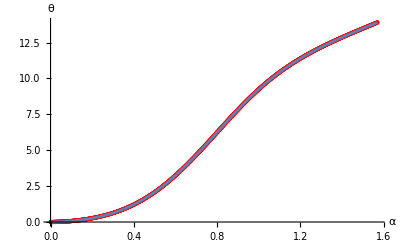

```mathematica
θaccs=χ*Accumulate[(-Dτs*uτs+Drs*urs)*fmtoIGeV*dαs];(*dimensionless*)
θacc=Interpolation[Transpose@{αs,θaccs}];
Show[
ListPlot[Transpose@{αs,θaccs},PlotStyle->{Directive[Red,PointSize[Medium]]},AxesLabel->{α,θ}],
Plot[θacc[α],{α,0,Pi/2},AxesLabel->{α,θ}]
]
```

The result can now be used to define the pi+- fields on the freezeout surface.

```mathematica
πp[n_,α_]=Sqrt[n]*Exp[I*θacc[α]]
πm[n_,α_]=Conjugate[πp[n,α]]
π1[n_,α_]=Sqrt[2]*Re@πp[n,α];
π2[n_,α_]=-Sqrt[2]*Im@πp[n,α];
```

ⅇ^(ⅈ InterpolatingFunction[…][α]) √n

ⅇ^(-ⅈ Conjugate[InterpolatingFunction[…][α]]) Conjugate[√n]

## Compute the Fourier Spectrum of the Source

First, define a set of helper functions. These depend on the (transverse) momentum p_ and the coordinate α_ on the Freezeout surface. Eventually we wish to integrate over the Freezeout surface. The dependence on p_ can be substituted by explicit evaluation on a (nicely resolved) grid in momentum space. The dependence on α_ must remain symbolic, since we wish to numerically integrate over α_ using NIntegrate.

```mathematica
ω[p_]=Sqrt[p^2+mπ^2];(*in GeV (p in GeV) *)
J0rp[α_,p_]=BesselJ[0,r[α]*p*GeVtoIfm];(*dimensionless*)
J1rp[α_,p_]=BesselJ[1,r[α]*p*GeVtoIfm];(*dimensionless*)
Y0tw[α_,p_]=BesselY[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
Y1tw[α_,p_]=BesselY[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J0tw[α_,p_]=BesselJ[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J1tw[α_,p_]=BesselJ[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)

H1[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p]);(*dimensionless*)
H2[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*J0rp[α,p]*ω[p]*(-Y1tw[α,p]+I*J1tw[α,p]);

G1[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]-I*J0tw[α,p]);(*dimensionless*)
G2[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]-I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*J0rp[α,p]*ω[p]*(-Y1tw[α,p]-I*J1tw[α,p]);(*dimensionless*)
```

NOTATION: an object named "fps" with f some quantity represents a function f[p_,...] with the p_-dependence evaluated explicitly on the momentum grid given by "ps".

```mathematica
ps=linspace[0,2,50];
Print[Min[ps]," to ",Max[ps], " GeV"]
```

0 to 2 GeV

The most ressource heavy computation happens here, due to the use of NIntegrate. The routine (probably) uses more and more subdivisions for the large-p_ components in H(1/2)ps.

WHY USE NINTEGRATE AND INTERPOLATED FUNCTIONS? Discrete Fourier Transform, say  on  an  Interval [0, L], discretized  with  N  points, shows  and  alias  effect  and  is  valid  only  up  to  the  Nyquist  frequency  (~ momentum)  (2?)  Nπ/L  and  the  spectrum  will  then  continue  periodically  (just  as  the  real  space  function  will, if  calculated  from  discretized  momentum  grid . There  will  thus  be  no  convergence  to  0  for  large  momenta . It  is  not  immediately  clear  to  me  how  this  effect  is  altered  when  using  Bessel  functions  and  the  integral  measure  in  polar  coordinates, but  qualitatively  this  should  prevent  convergence  to  0  of  the  spectrum  for  large  p, which  would  be  necessary  for  a  physical  spectrum . 
    
    One  could  simply  apply  a  finer  discretization  in  real  space  (= finer  mesh  of  αs), but  I  expect  the  effect  to  be  worse  for  larger  momenta . The  routine  NIntegrate  automatically  chooses  and  refines  the  grid  of  αs  in  real  space, until  the  integral  has  converged  sufficiently  well . For  low  p_  it  is  expected  that  the  grid  specified  by  the  raw  data  is  enough . For  large  p_  a  finer  grid  should  be  chosen . We  should  thus  provide  (interpolated)  functions  of  α_  such  that  this  refinement  through  the  integration  routine is dynamically possible .

## All of the Above In a Single Function

```mathematica
(*
π0=...;
Dπ0=σ0[α]*χ*(-Dr[α]*uτ[α]+Dτ[α]*ur[α]);
*)
ComputeSourceSpectr[ps_,f_,Df_]:=Module[{H1ps,H2ps,spectrps},
(*
f is supposed to be the π-field, Df it's perpendiculat derivative, 
Df = r'*D[f,τ]+τ'*D[f,r]

The name π is protected!!!
*)
H1ps[α_]=H1[α,ps];
H2ps[α_]=H2[α,ps];

spectrps=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*H1ps[α]+f[α]*H2ps[α]),{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
spectrps
]
ComputeSourceSpectrAnti[ps_,f_,Df_]:=Module[{H1ps,H2ps,spectrps},
(*
f is supposed to be the π-field, Df it's perpendiculat derivative, 
Df = r'*D[f,τ]+τ'*D[f,r]

The name π is protected!!!
*)
G1ps[α_]=G1[α,ps];
G2ps[α_]=G2[α,ps];

spectrps=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*G1ps[α]+f[α]*G2ps[α]),{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
spectrps
]
```

```mathematica
ps=linspace[0,1,100];
Jπ1spec=ComputeSourceSpectr[ps,π1[1,#]&,π2[1,#]*χ*(-Dr[#]*uτ[#]+Dτ[#]*ur[#])&];
Jπ2spec=ComputeSourceSpectr[ps,π2[1,#]&,-1*π1[1,#]*χ*(-Dr[#]*uτ[#]+Dτ[#]*ur[#])&];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -794.182-567.943 ⅈ and 0.0234087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -792.513-569.013 ⅈ and 0.0231736 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -788.109-568.999 ⅈ and 0.0210016 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 1118.71-1260.88 ⅈ and 0.0470384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 1131.-1231.97 ⅈ and 0.0466039 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 1159.28-1145.73 ⅈ and 0.0416593 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

This does exactly the same as before:

```mathematica
Jπ1specfinal[θ0_]=Cos[θ0]*Jπ1spec+Sin[θ0]*Jπ2spec;
Jπ2specfinal[θ0_]=Cos[θ0]*Jπ2spec-Sin[θ0]*Jπ1spec;
```

```mathematica
Manipulate[
ListLogPlot[{Transpose@{ps,Abs@(Jπ1spec)^2},
Transpose@{ps,Abs@(Jπ2spec)^2},
Transpose@{ps,Abs@(Jπ1specfinal[θ0]-I*Jπ2specfinal[θ0])^2},
Transpose@{ps,Abs@(Jπ1specfinal[θ0]+I*Jπ2specfinal[θ0])^2},
Transpose@{ps,Abs@(Jπ1specfinal[θ0]-I*Jπ2specfinal[θ0])^2+Abs@(Jπ1specfinal[θ0]+I*Jπ2specfinal[θ0])^2}}],
{θ0,0,Pi/2}]
```

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jπ1spec]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jπ2spec]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jπ1specfinal[0.]-ⅈ Jπ2specfinal[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jπ1spec]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jπ2spec]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jπ1specfinal[0.]-ⅈ Jπ2specfinal[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
ps=linspace[0,1,100];
Jπpspec=ComputeSourceSpectr[ps,πp[1,#]&,χ*πp[1,#]*(-Dr[#]*uτ[#]+Dτ[#]*ur[#])&];
JπpspecAnti=ComputeSourceSpectrAnti[ps,πp[1,#]&,χ*πp[1,#]*(-Dr[#]*uτ[#]+Dτ[#]*ur[#])&];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -1884.23-971.477 ⅈ and 0.0406081 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -1836.83-984.513 ⅈ and 0.0376291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -1698.83-1011.66 ⅈ and 0.0339363 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 515.015-385.545 ⅈ and 0.0387882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 494.376-400.13 ⅈ and 0.0373467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 431.173-439.423 ⅈ and 0.03325 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

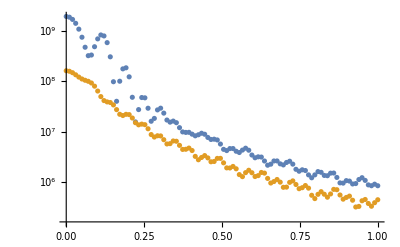

```mathematica
ListLogPlot[{Transpose@{ps,Abs@(Jπpspec)^2+Abs@(JπpspecAnti)^2},Transpose@{ps,Abs@(JπpspecAnti)^2}}]
```

## Compare to Alice Data

```mathematica
Alicedatatxt=Import[StringJoin[NotebookDirectory[],"data/HEPData-ins1222333-v1-Table_1.csv"],"Text"];
(*Alicedata=ImportString[StringReplace[StringReplace[Alicedatatxt,RegularExpression["\n+"]->"\n"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV"];*)
Alicedata=ImportString[StringReplace[Alicedatatxt,StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV","IgnoreEmptyLines"->True];
MatrixForm[Alicedata];
titles=Alicedata[[1]];
enumeratedtitles=Transpose[{Range[Length[titles]],titles}]
πplus=Alicedata[[2;;42]];
πminus=Alicedata[[44;;]];
aliceps=(Transpose@πplus)[[1]];
aliceyieldplus=(Transpose@πplus)[[4]];
aliceyieldminus=(Transpose@πminus)[[4]];
Fluidumdata=Import[StringJoin[NotebookDirectory[],"data/pionSpectra.txt"],"CSV"];
```

{{1,PT [GEV]},{2,PT [GEV] LOW},{3,PT [GEV] HIGH},{4,(1/Nev)*(1/(2*PI*PT))*D2(N)/DPT/DYRAP [GEV**-2]},{5,stat +},{6,stat -},{7,sys +},{8,sys -},{9,sys,normalization uncertainty +},{10,sys,normalization uncertainty -}}

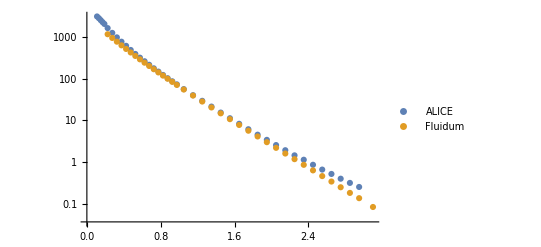

```mathematica
ListALICE=Transpose@{aliceps,aliceyieldplus+aliceyieldminus};
ListFluidum=Transpose@{Fluidumdata[[1]],2*Fluidumdata[[2]]};
ListLogPlot[
{ListALICE,
ListFluidum},
PlotLegends->{"ALICE","Fluidum"}
]
```

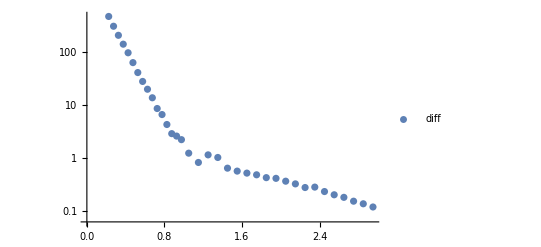

```mathematica
diff=(Transpose@ListALICE)[[2]][[6;;]]-(Transpose@ListFluidum)[[2]][[;;-2]];
Listdiff=Transpose@{(Transpose@ListALICE)[[1]][[6;;]],diff};
ListLogPlot[Listdiff,PlotLegends->{"diff"}]
```

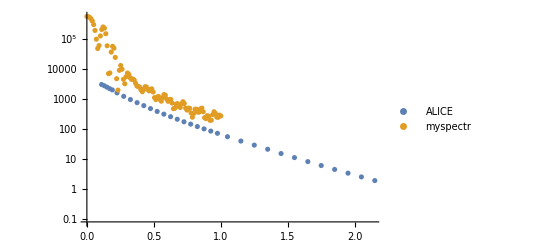

```mathematica
Quiet[
{
ListLogPlot[
{ListALICE,Transpose@{ps,1/(2*2*Pi)^3*Abs[Jπ2spec]^2}},
PlotLegends->{"ALICE","myspectr"}
]},{Transpose::nmtx}]
```

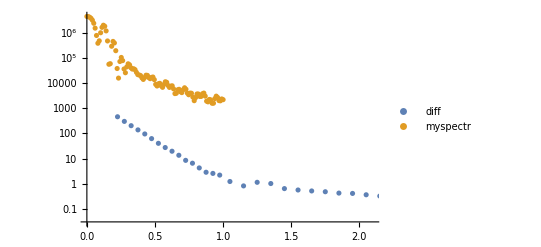

```mathematica
ListLogPlot[
{Listdiff,Transpose@{ps,1/(2*Pi)^3*Abs[Jπ2spec]^2}},
PlotLegends->{"diff","myspectr"}
]
```